```mathematica
MAXLSE[a_,x_]:=a Log[Total[Map[Exp,x/a]]]
```

```mathematica
ABSLSE[a_,x_]:=2MAXLSE[a,{x,0}]-x
```

```mathematica
N[MAXLSE[1/10,{1,2,3}],20]
```

3.0000045400960276913

```mathematica
ABSLSE[1/100,-0.01]
```

0.0162652

```mathematica
ABSSQRT[a_,x_]:=Sqrt[x^2+a^2]
```

```mathematica
MAXSQRT[a_,x_,y_]:=(x+y+ABSSQRT[a,x-y])/2
```

```mathematica
N[MAXSQRT[1/10,MAXSQRT[1/10,1,2],3],20]
```

3.0024999844915075483

```mathematica
ABSSQRT[1/100,-0.01]
```

0.0141421

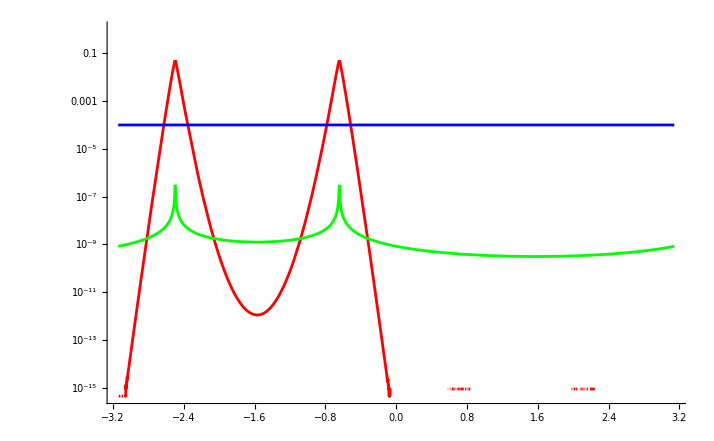

```mathematica
LogPlot[{MAXLSE[0.08,{4Sin[x]+4,-Sin[x]+1}]-Max[4Sin[x]+4,-Sin[x]+1],MAXSQRT[0.0001,4Sin[x]+4,-Sin[x]+1]-Max[4Sin[x]+4,-Sin[x]+1],0.0001},{x,-Pi,Pi},PlotStyle->{Red,Green,Blue},PlotRange->{Automatic,{0,1}}]
```

```mathematica
m23=({{Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3], -Cos[t2] Sin[t1], Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3]}, {Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3], Cos[t1] Cos[t2], -Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]}, {-Cos[t2] Sin[t3], Sin[t2], Cos[t2] Cos[t3]}});
```

```mathematica
m23//MatrixForm
```

(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3] | -Cos[t2] Sin[t1] | Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3]
Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3] | Cos[t1] Cos[t2] | -Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]
-Cos[t2] Sin[t3] | Sin[t2] | Cos[t2] Cos[t3])

```mathematica
m231=Abs[m23[[1]][[1]]]+Abs[m23[[1]][[2]]]
```

Abs[Cos[t2] Sin[t1]]+Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]]

```mathematica
m232=Abs[m23[[2]][[1]]]+Abs[m23[[2]][[2]]]
```

Abs[Cos[t1] Cos[t2]]+Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]]

```mathematica
m233=Abs[m23[[3]][[1]]]+Abs[m23[[3]][[2]]]
```

Abs[Sin[t2]]+Abs[Cos[t2] Sin[t3]]

```mathematica
f23=Max[m231,m232,m233]
```

Max[Abs[Sin[t2]]+Abs[Cos[t2] Sin[t3]],Abs[Cos[t1] Cos[t2]]+Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]],Abs[Cos[t2] Sin[t1]]+Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]]]

```mathematica
Plot3D[f23/.{t2->0},{t1,-Pi/2,Pi/2},{t3,-Pi/2,Pi/2},Exclusions->False,PlotPoints->50,MaxRecursion->4,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
table23t3=Table[f23/.{t1->Pi/4+m Pi /40,t2->0},{m,0,10}];
```

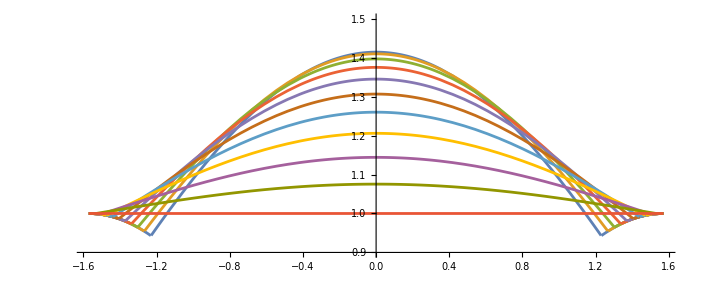

```mathematica
Plot[table23t3,{t3,-Pi/2,Pi/2},PlotRange->{Automatic,{0.9,1.5}},AspectRatio->Automatic]
```

```mathematica
FindMinimum[f23/.{t2->0},{t1,Pi/4+0.1},{t3,Pi/4+0.1}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.952969,{t1→0.716921,t3→1.26289}}

```mathematica
1/0.9529686832455019
```

1.04935

```mathematica
N[Sqrt[9/8]]
```

1.06066

```mathematica
f23/.{t1->0.7169213677889057,t2->0,t3->1.2628850542469452}
```

0.952969

```mathematica
Show[ListPointPlot3D[{{Pi/4+0.1,Pi/4+0.1,f23/.{t1->Pi/4+0.1,t2->0,t3->Pi/4+0.1}},{0.7169213677889057,1.2628850542469452,f23/.{t1->0.7169213677889057,t2->0,t3->1.2628850542469452}}},PlotRange->{Automatic,Automatic,{0,Pi/2}},Filling->Bottom,AxesLabel->{t1,t3}],Plot3D[f23/.{t2->0},{t1,0,Pi/2},{t3,Pi/4,3Pi/4},Exclusions->False,PlotPoints->50,MaxRecursion->4,AxesLabel->Automatic]]
```

-Graphics3D-

```mathematica
f23c=f23/.{t1->0.7169213677889057,t2->0,t3->1.2628850542469452}
```

0.952969

```mathematica
Table[(f23-f23c)/.{t1->0.7169213677889057+e1/20,t2->0,t3->1.2628850542469452+e3/20},{e3,-1,1},{e1,-1,1}]//MatrixForm
```

(0.0494576 | 0.0310463 | 0.0101754
0.0202303 | 0. | -6.88598×10^-9
0.0139562 | 0.0139562 | 0.0139562)

```mathematica
sg=1/20;Show[ListPointPlot3D[Flatten[Table[{0.7169213677889057+e1 sg,1.2628850542469452+e3 sg,f23/.{t1->0.7169213677889057+e1 sg,t2->0,t3->1.2628850542469452+e3 sg}},{e1,-1,1},{e3,-1,1}],1],PlotRange->{Automatic,Automatic,Automatic},Filling->Bottom,AxesLabel->{t1,t3},AspectRatio->1],Plot3D[f23/.{t2->0},{t1,0,Pi/2},{t3,Pi/4,3Pi/4},Exclusions->False,PlotPoints->50,MaxRecursion->5,AxesLabel->Automatic],ViewPoint->Above,ImageSize->Full]
```

-Graphics3D-

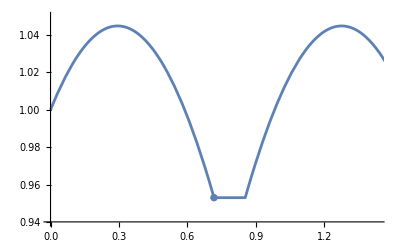

```mathematica
Show[ListPlot[{{0.7169213677889057,f23/.{t1->0.7169213677889057,t2->0,t3->1.2628850542469452}}},PlotRange->{Automatic,{0.94,1.05}}],Plot[f23/.{t2->0,t3->1.2628850542469452},{t1,0,Pi/2},Exclusions->False],ImageSize->Full]
```

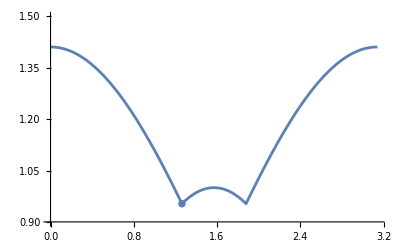

```mathematica
Show[ListPlot[{{1.2628850542469452,f23/.{t1->0.7169213677889057,t2->0,t3->1.2628850542469452}}},PlotRange->{{0,Pi},{0.9,1.5}}],Plot[f23/.{t1->0.7169213677889057,t2->0},{t3,0,Pi},Exclusions->False],ImageSize->Full]
```

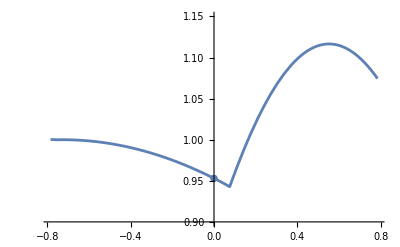

```mathematica
th=-25Pi/180;Show[ListPlot[{{0,f23/.{t1->0.7169213677889057,t2->0,t3->1.2628850542469452}}},PlotRange->{{-Pi/4,Pi/4},{0.9,1.15}}],Plot[f23/.{t1->0.7169213677889057+e Cos[th],t2->0,t3->1.2628850542469452+e Sin[th]},{e,-Pi/4,Pi/4},Exclusions->False],ImageSize->Full]
```

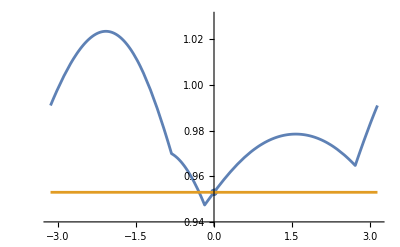

```mathematica
e=0.1;thr=Pi;Show[ListPlot[{{0,f23/.{t1->0.7169213677889057+e,t2->0,t3->1.2628850542469452}}},PlotRange->{{-thr,thr},{0.94,1.03}}],Plot[{f23/.{t1->0.7169213677889057+e Cos[th],t2->0,t3->1.2628850542469452+e Sin[th]},f23/.{t1->0.7169213677889057,t2->0,t3->1.2628850542469452}},{th,-thr,thr},Exclusions->False],ImageSize->Full]
```

```mathematica
Clear[th];FindMinimum[(f23/.{t1->0.7169213677889057+e Cos[th],t2->0,t3->1.2628850542469452+e Sin[th]})/.{e->0.1},{th,0}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.947393,{th→-0.179925}}

```mathematica
1/0.9473927894048706
```

1.05553

```mathematica
Sqrt[9/8]-1/0.9473927894048706
```

0.00513177

```mathematica
{t1->0.7169213677889057+e Cos[th],t2->0,t3->1.2628850542469452+e Sin[th]}/.{e->0.1,th->-0.17992481208118702}
```

{t1→0.815307,t2→0,t3→1.24499}

```mathematica
f23/.{t1->0.8153070828757254,t2->0,t3->1.2449894942709303}
```

0.947393

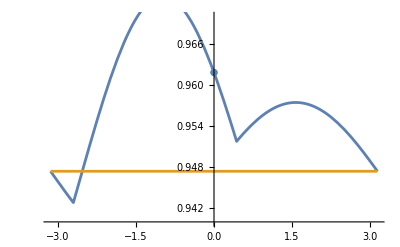

```mathematica
e=0.033;thr=Pi;Show[ListPlot[{{0,f23/.{t1->0.8153070828757254+e,t2->0,t3->1.2449894942709303}}},PlotRange->{{-thr,thr},{0.94,0.97}}],Plot[{f23/.{t1->0.8153070828757254+e Cos[th],t2->0,t3->1.2449894942709303+e Sin[th]},f23/.{t1->0.8153070828757254,t2->0,t3->1.2449894942709303}},{th,-thr,thr},Exclusions->False],ImageSize->Full]
```

```mathematica
|
```

```mathematica
Clear[th];FindMinimum[(f23/.{t1->0.8153070828757254+e Cos[th],t2->0,t3->1.2449894942709303+e Sin[th]})/.{e->0.033},{th,-Pi}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.942814,{th→-2.70298}}

```mathematica
1/0.942814
```

1.06065

```mathematica
Sqrt[9/8]-1/0.942814
```

5.57819×10^-6

```mathematica
{t1->0.8153070828757254+e Cos[th],t2->0,t3->1.2449894942709303+e Sin[th]}/.{e->0.033,th->-2.702976682084363}
```

{t1→0.785431,t2→0,t3→1.23097}

```mathematica
f23/.{t1->0.8153070780966387,t2->0,t3->1.2528850542469463}
```

0.94989

```mathematica
1/(f23/.{t1->0.7854308526837801,t2->0,t3->1.2309748280416584})
```

1.06065

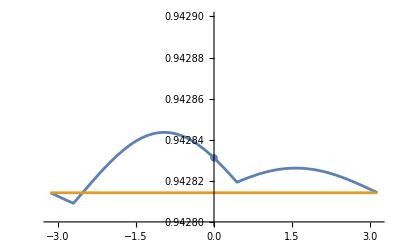

```mathematica
e=0.000036;thr=Pi;Show[ListPlot[{{0,f23/.{t1->0.7854308526837801+e,t2->0,t3->1.2309748280416584}}},PlotRange->{{-thr,thr},{0.9428,0.9429}}],Plot[{f23/.{t1->0.7854308526837801+e Cos[th],t2->0,t3->1.2309748280416584+e Sin[th]},f23/.{t1->0.7854308526837801,t2->0,t3->1.2309748280416584}},{th,-thr,thr},Exclusions->False],ImageSize->Full]
```

```mathematica
Clear[th];FindMinimum[(f23/.{t1->0.7854308526837801+e Cos[th],t2->0,t3->1.2309748280416584+e Sin[th]})/.{e->0.000036},{th,-Pi}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.942809,{th→16.1485}}

```mathematica
1/0.9428090614423901
```

1.06066

```mathematica
Sqrt[9/8]-1/0.9428090614423901
```

2.23429×10^-8

```mathematica
m231SQRT[eps_]:=ABSSQRT[eps,m23[[1]][[1]]]+ABSSQRT[eps,m23[[1]][[2]]]
```

```mathematica
m232SQRT[eps_]:=ABSSQRT[eps,m23[[2]][[1]]]+ABSSQRT[eps,m23[[2]][[2]]]
```

```mathematica
m233SQRT[eps_]:=ABSSQRT[eps,m23[[3]][[1]]]+ABSSQRT[eps,m23[[3]][[2]]]
```

```mathematica
f23SQRT[eps_]:=MAXSQRT[eps,MAXSQRT[eps,m231SQRT[eps],m232SQRT[eps]],m233SQRT[eps]];
```

```mathematica
eps=0.02;Plot3D[f23SQRT[eps]/.{t2->0},{t1,-Pi/2,Pi/2},{t3,-Pi/2,Pi/2},Exclusions->False,PlotPoints->100,MaxRecursion->4,AxesLabel->Automatic]
```

-Graphics3D-

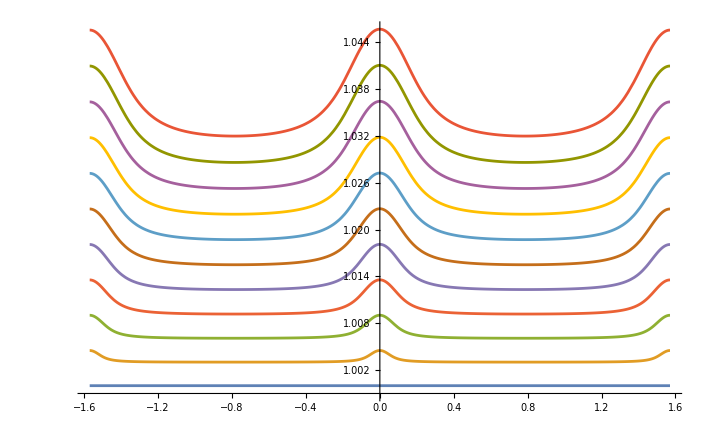

```mathematica
eps=0.03;table23t3SQRT=Table[f23SQRT[m /10eps]/.{t1->0,t2->0},{m,0,10}];Plot[table23t3SQRT,{t3,-Pi/2,Pi/2},PlotRange->{{-Pi/2,Pi/2},{0.999,Automatic}}]
```

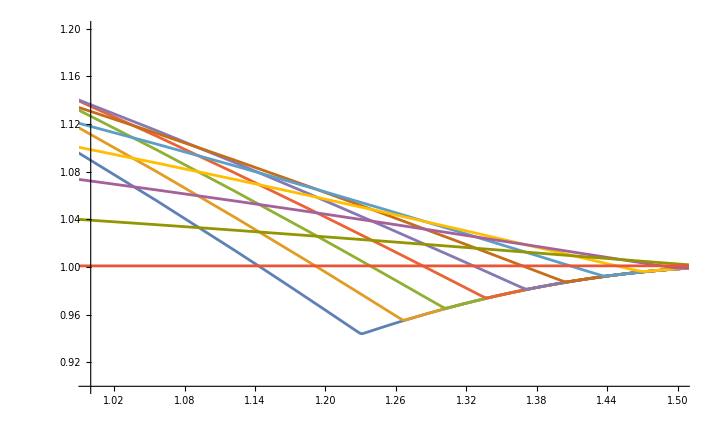

```mathematica
eps=0.001;table23t3SQRT=Table[f23SQRT[eps]/.{t1->Pi/4+m Pi /40,t2->0},{m,0,10}];Plot[table23t3SQRT,{t3,-Pi/2,Pi/2},PlotRange->{{1.0,1.5},{0.9,1.2}},AspectRatio->Automatic]
```

```mathematica
FindMinimum[f23SQRT[eps]/.{t2->0},{t1,0.4},{t3,0.4}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.944115,{t1→-5.49779,t3→5.05237}}

```mathematica
(1/f23/.{t1->-5.497787143335392,t2->0,t3->5.052370279970468})-Sqrt[9/8]
```

-0.000108279

```mathematica
FindMinimum[f23SQRT[eps]/.{t2->0},{t1,Pi/4},{t3,Pi/4}]
```

{0.944115,{t1→0.785398,t3→1.23082}}

```mathematica
(1/f23/.{t1->0.7853981633884802,t2->0,t3->1.230815027221493})-Sqrt[9/8]
```

-0.000108279

```mathematica
FindMinimum[f23SQRT[eps]/.{t2->0},{t1,Pi/4+0.1},{t3,Pi/4+0.1}]
```

{0.944115,{t1→0.785398,t3→1.23082}}

```mathematica
{(1/f23/.{t1->0.785398163386233,t2->0,t3->1.2308150272285574}),N[Sqrt[9/8],10],(1/f23/.{t1->0.785398163386233,t2->0,t3->1.2308150272285574})-Sqrt[9/8]}//MatrixForm
```

(1.06055
1.060660172
-0.000108279)

```mathematica
Show[ListPointPlot3D[{{Pi/4+0.1,Pi/4+0.1,f23SQRT[eps]/.{t1->Pi/4+0.1,t2->0,t3->Pi/4+0.1}},{0.785398163386233,1.2308150272285574,f23SQRT[eps]/.{t1->0.785398163386233,t2->0,t3->1.2308150272285574}}},PlotRange->{Automatic,Automatic,{0,Pi/2}},Filling->Bottom,AxesLabel->{t1,t3}],Plot3D[f23SQRT[eps]/.{t2->0},{t1,0,Pi/2},{t3,Pi/4,3Pi/4},Exclusions->False,PlotPoints->50,MaxRecursion->4,AxesLabel->Automatic]]
```

-Graphics3D-

```mathematica
f23/.{t1->0.7853981634978824,t2->0,t3->1.2305385489586693}
```

0.94309

```mathematica
1/0.9430895996675074
```

1.06034

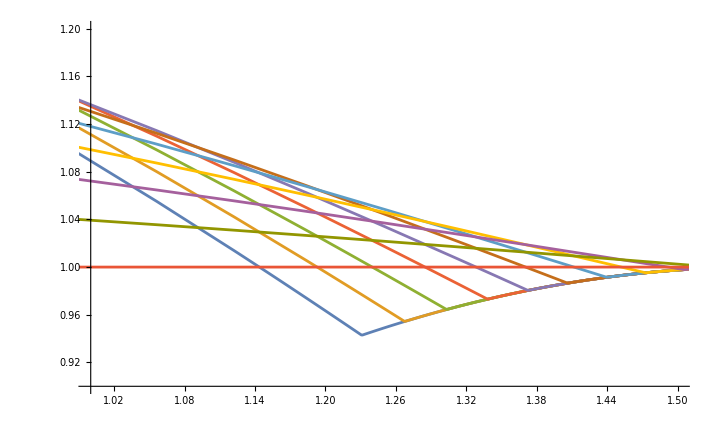

```mathematica
eps=0.000001;table23t3SQRT=Table[f23SQRT[eps]/.{t1->Pi/4+m Pi /40,t2->0},{m,0,10}];Plot[table23t3SQRT,{t3,-Pi/2,Pi/2},PlotRange->{{1.0,1.5},{0.9,1.2}},AspectRatio->Automatic]
```

```mathematica
FindMinimum[f23SQRT[eps]/.{t2->0},{t1,0.4},{t3,0.4}]
```

{0.94281,{t1→-10.2102,t3→8.19382}}

```mathematica
FindMinimum[f23SQRT[eps]/.{t2->0},{t1,Pi/4},{t3,Pi/4}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.94281,{t1→0.785398,t3→1.23096}}

```mathematica
(1/f23/.{t1->0.7853981634019855,t2->0,t3->1.230959270884052})-Sqrt[9/8]
```

-1.09845×10^-7

```mathematica
FindMinimum[f23SQRT[eps]/.{t2->0},{t1,Pi/4+0.1},{t3,Pi/4+0.1}]
```

{0.94281,{t1→0.785398,t3→1.23096}}

```mathematica
{(1/f23/.{t1->0.7853981633974711,t2->0,t3->1.2309592708962247}),N[Sqrt[9/8],10],(1/f23/.{t1->0.7853981633974711,t2->0,t3->1.2309592708962247})-Sqrt[9/8]}//MatrixForm
```

(1.06066
1.060660172
-1.09833×10^-7)